```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
l=50;
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,l}];
mpi=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/mpion.dat"]],{i,1,l}];
msigma=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/msigma.dat"]],{i,1,l}];
T=Table[i,{i,50,130}];
mub=Flatten[Table[i*5,{i,1,l}]];
data=Flatten[Table[{x=mub[[j]],y=T[[i]],fpiall[[j]][[i]]},{i,1,Length[T]},{j,1,50}],1];
data2=Flatten[Table[{x=mub[[j]],y=T[[i]],1/msigma[[j]][[i]]},{i,1,Length[T]},{j,1,50}],1];
```

```mathematica
ListDensityPlot[data2,PlotRange->{All,All,{0,1}}]
```

-Graphics-

```mathematica
mub2=Flatten[{mub,600}];
Tc2=Flatten[{Tc,57.916430}];
```

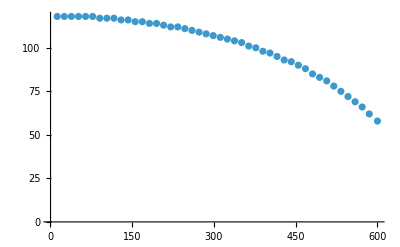

```mathematica
ListPlot[Transpose[{mub2,Tc2}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub2,Tc2}],a+b x^2+c x^4,{a,b,c},x]
```

{a→117.955,b→-0.000101378,c→-1.76668×10^-10}

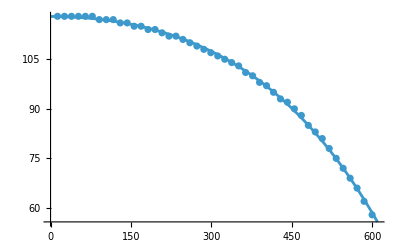

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,610}],ListPlot[Transpose[{mub2,Tc2}]]]
```

```mathematica
mub={0,100,200,300,400,500,550,575,600};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
Export["pb.dat",phaseboundary]
```

pb.dat

```mathematica
mub2=Table[i,{i,0,600,10}];
Tc2=Table[{mub2[[i]],a+b mub2[[i]]^2+c mub2[[i]]^4/.fitpd},{i,1,Length[mub2]}];
Export["pb2nd.dat",Tc2]
```

pb2nd.dat